```mathematica
datos=Import["/Users/miguel/Desktop/Delfín/Mathematica/datos.txt","Table"];
datos // TableForm



vertices={{0,5000,1},{2500,5000,2},{4000,5000,3},{5000,5000,4},{0,3000,5},{2000,3000,6},{2500,3000,7},{4000,2750,8},{5000,2750,9},{2000,2000,10},{2500,2000,11},{3750,2000,12},{4000,2000,13},{5000,2000,14},{3750,1250,15},{5000,1250,16},{0,500,17},{2000,500,18},{0,0,19},{2000,0,20},{3750,0,21},{5000,0,22}};
aristas={{1,2,2500},{2,3,1500},{3,4,1000},{5,6,2000},{6,7,500},{8,9,1000},{10,11,500},{11,12,1250},{12,13,250},{13,14,1000},{15,16,1250},{17,18,2000},{19,20,2000},{20,21,1750},{21,22,1250},{4,9,2250},{9,14,750},{14,16,750},{16,22,1250},{3,8,2250},{8,13,750},{12,15,750},{15,21,1250},{2,7,2000},{7,11,1000},{6,10,1000},{10,18,1500},{18,20,500},{1,5,2000},{5,17,2500},{17,19,500}};
```

10 | 5000 | 5000 | 
2000 | 3000 | 2500 | 2000
4000 | 2750 | 5000 | 2000
0 | 5000 | 2500 | 3000
2500 | 5000 | 4000 | 2000
4000 | 5000 | 5000 | 2750
2000 | 2000 | 3750 | 0
3750 | 2000 | 5000 | 1250
3750 | 1250 | 5000 | 0
0 | 500 | 2000 | 0
0 | 3000 | 2000 | 500
7 |  |  |

Aristas No Dirigidas, Pesos de Aristas y Coordenadas de Vértices

```mathematica
nEdges=Map[#_⟦1⟧<->#_⟦2⟧&,aristas];
```

```mathematica
eWeigth=Map[#_⟦3⟧&,aristas];
```

```mathematica
coord=Map[Take[#,2]&,vertices];
```

Calculo de Cantidad de Aristas y Pesos de Aristas

```mathematica
Length[nEdges];
Length[eWeigth];
Length[coord];
```

Relación de Aristas con sus Pesos

```mathematica
eEdges=Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]];
```

Construcción del Gráfo a partir de las Aristas, Pesos y Coordenadas

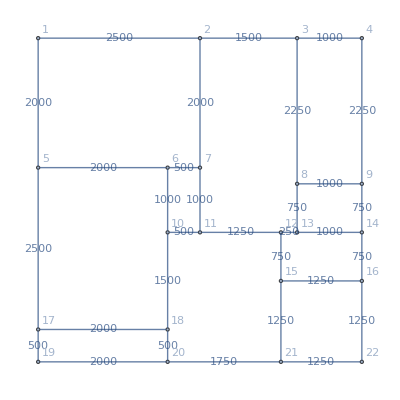

```mathematica
g=Graph[nEdges,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->eWeigth,VertexCoordinates->coord,EdgeLabels->eEdges]
```

Generacion de la lista de poligonos

```mathematica
listaDeVertices = VertexList[g];
coordenadas=GraphEmbedding[g]
g;
datos // TableForm;



poligonos={};
vertice1 =0;
coorx1=0;
coorx2 =0;
vertice2 =0;
coory1=0;
coory2=0;
vertice3 =0;
vertice4=0;

For[i=2, i<Length[datos], i++,
For[j=1, j≤ 2, j++,
If[j==  1,
vertice1 =Position[coordenadas,{datos[[i]][[1]],datos[[i]][[2]]}][[1]][[1]];
coory1= datos[[i]][[2]];
coorx2 =datos[[i]][[1]];
,
vertice2=Position[coordenadas,{datos[[i]][[3]],datos[[i]][[4]]}][[1]][[1]];
coorx1 = datos[[i]][[3]];
coory2= datos[[i]][[4]];
];
vertice3 = Position[coordenadas,{coorx1,coory1}][[1]][[1]];
(*vertice4 = Position[coordenadas,{coorx2,coory2}][[1]][[1]];*)
];
(*AppendTo[poligonos,{vertice1<->vertice3,vertice3<->vertice2,vertice2<->vertice4,vertice4<->vertice1}]*)
]


poligonos
```

{{0,5000},{2500,5000},{4000,5000},{5000,5000},{0,3000},{2000,3000},{2500,3000},{4000,2750},{5000,2750},{2000,2000},{2500,2000},{3750,2000},{4000,2000},{5000,2000},{3750,1250},{5000,1250},{0,500},{2000,500},{0,0},{2000,0},{3750,0},{5000,0}}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{}